```mathematica
rawfig2a=Import[NotebookDirectory[]<>"fig2a_data.csv","CSV"];
```

Import::nffil: File /Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/New_Revised_Figures/Fig_SI_fixtime/fig2a_data.csv not found during Import.

## Equilibrium calculation

```mathematica
A[u_,α_,γ_]:=(u/(1-u)+1-γ)/(α γ);
equilibrium[r_,β_,u_,α_,γ_]:=1/(((r+1)/(A[u,α,γ] (r-1)+r)-1)^(1/β)+1);
```

```mathematica
q2=3;q1=2;β=.;u=0;α=0.8;
Manipulate[eq2a=Plot[equilibrium[q2/q1,β,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.01]],Frame->True,AspectRatio->1],{β,0.001,2}]
```

```mathematica
eq2a=Plot[equilibrium[q2/q1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1];
```

## Fig2a

```mathematica
rawfig2a=Import[NotebookDirectory[]<>"fig2a_data.csv","CSV"];
```

```mathematica
heat2a=ListDensityPlot[rawfig2a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

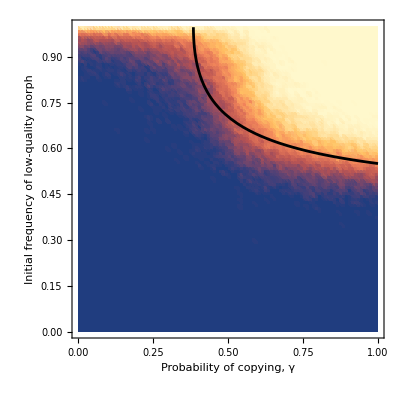

```mathematica
Show[heat2a,eq2a]
```

## Fig2b

```mathematica
rawfig2b=Import[NotebookDirectory[]<>"fig2b_data.csv","CSV"];
```

```mathematica
heat2b=ListDensityPlot[rawfig2b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

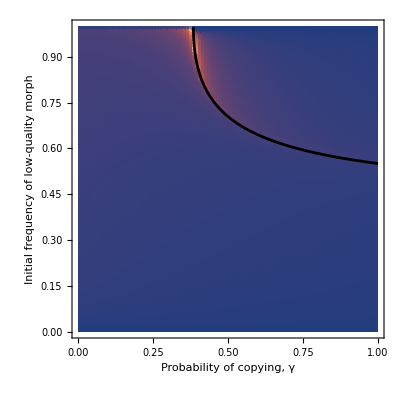

```mathematica
Show[heat2b,eq2a]
```

## Fig 2c

```mathematica
rawfig2c=Import[NotebookDirectory[]<>"fig2c_data.csv","CSV"];
```

```mathematica
heat2c=ListDensityPlot[rawfig2c⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Absolute difference in modified qualities",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

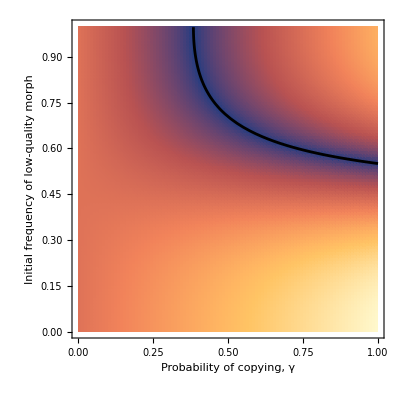

```mathematica
Show[heat2c,eq2a]
```